# CHEM304 Mathematica Tutorial and Reference Guide

## Tutorial

### Basic Syntax (do throughout, make sure talk about these)

Lists (making, indexing, using lists as an input, transposing, riffling, other function names)
brackets
spaces
sectioning/organization/not code/input sections
semicolons

### Variables

Cells containing expressions will evaluate when the cell is run. To evaluate the following cell, click on it and press shift and enter at the same time. Try to predict what the expression is equal to, which will also be the output of the cell

```mathematica
2+2
```

Variables allow us to store data temporarily. This data can take many forms, but one of the simplest forms is a number. See how we can set a variable “x” equal to one in the following cell

```mathematica
x=1;
```

Now that we have defined our variable, we can use it elsewhere in our code. The next cell contains an expression using x. Since the line does not end in a semicolon, we will be able to see the output, or in other words what the expression is equal to. Try to predict the output of the following cell.

```mathematica
x + 4
```

We can also change variables after they are first defined. The next cell changes the value of x, and then uses it in another expression. Try to predict the output of the following cell.

```mathematica
x=3;
x
x*5
```

We can also define new variables using previous variables, additionally, variables can also be defined with a colon and equal sign. Try to predict the output of the following cell.

```mathematica
y:=x+2;
y+x
```

We defined a new variable “y”, which is equal to “5”.
We can also store other kinds of data in variables. For example we can store letters in a variable, and when we do so this kind of variable is called a string. The next cell defines string variable.

```mathematica
authorName = "RowanAndLogan";
```

Another important kind of data that can be stored in variables is lists. The next cell defines a list of four numbers.

```mathematica
numberList = {4,0,2.5,10};
```

There are a couple of other ways to view a list. The first is TableForm which prints the elements of the list and arranges them in a table (you can specify other properties of the table like headings, spacings, direction, depth, etc. if you wanted to). Additionally, you can also print out the list as a matrix using MatrixForm.

```mathematica
TableForm[numberList];
```

```mathematica
MatrixForm[numberList];
```

One thing or “element” from the list can be accessed using an integer in double brackets. The elements are indexed by integers starting at 1. For our “numberList” it is indexed by 1, 2, 3, and 4. Try to predict the output of the following cell.

```mathematica
numberList[[3]]
```

Now it’s your turn to try. Place an integer in the double brackets in the following cell to try to get the output of “10”.

```mathematica
numberList[[(*integer*)]]
```

Mathematica can also treat your list as a vector. If we think of our numberList like this, then it is a four dimension vector. We can calculate the dot product of our vector with itself, as seen in the following cell.

```mathematica
numberList.numberList
```

We can manually write out this same calculation, as seen in the following cell. Try to fill in the missing integer.

```mathematica
numberList[[1]]^2+numberList[[(*integer*)]]^2+numberList[[3]]^2+numberList[[4]]^2
```

### Operators

#### Arithmetic

Mathematica can easily be used for basic math operations just like any other basic scientific calculator. Try running the following cells that contain operations

Addition:

```mathematica
7+5
```

Subtraction:

```mathematica
7-5
```

Multiplication:

```mathematica
7*5
```

Division

```mathematica
7/5
```

Exponents

```mathematica
7^5
```

```mathematica
7^5
```

Factorials

```mathematica
7!
```

Logarithms

```mathematica
Log10[100](*Log10 specifies a base 10 logarithm*)
```

```mathematica
Log[10,100](*you can also specify the base in the logarithm*)
```

```mathematica
Log[E^2](*Mathematica assumes a natural logarithm with no other base specification*)
```

```mathematica
an=E^5;
```

```mathematica
Log[an]
```

Parentheses can be used to specify an order of operations. Try to predict the output of both the following cells:

```mathematica
(2+3)*(1+1)
```

```mathematica
2+(3*1)+1
```

Parentheses can also be used to specify what is in an exponential. Try to predict the output of both the following cells:

```mathematica
2^(2+1)
```

```mathematica
(2^2)+1
```

#### Calculus

```mathematica
Clear[x,y]
```

Mathematica can even be used to take derivates in the following way. Try running the following cell:

```mathematica
D[2x^2,x]
```

4 x

Now predict the output of the following cell:

```mathematica
D[30y,y]
```

You can see that for a simple derivative like the one above: the function that you want to take the derivative of is on the inside left of the brackets, while the variable that you are taking the derivative with respect to is on the inside right of the brackets.

You can even take the second derivative of something. Try to predict the output of the following cell:

```mathematica
D[3 x^3,{x,2}]
```

```mathematica
D[5x y, x](*you can think of this on some level as taking a partial derivative of the function with respect to x*)
```

Mathematica lets you integrate functions. Try running the following cell:

```mathematica
Integrate[x,{x,0,1}]
```

Try to predict the output of the following cell:

```mathematica
Integrate[x^2,{x,0,y}]
```

As you can see above: the integrand is on the inside left of the brackets, and the variable you are taking the integral over is expressed as the first entity within the curly braces with its respective lower and upper bounds next to it in the curly braces.

There is a handy feature that lets you solve equalities for variables:

```mathematica
Solve[5x==15,x]
```

Mathematica can also handle trigonometric functions. It is important to note that the default unit for these calculations are in radians rather than degrees. Predict and run the following cells:

```mathematica
Sin[Pi/2]
```

```mathematica
Cos[Pi/2]
```

Mathematica is also very useful for probability calculations. Here we have defined a list of steps that someone takes while walking their dog each day:

```mathematica
stepsWalked={5108,6576,2363,1247,6816,3289,2764,2687,2782,5020};
```

We can take the mean using Mathematica to find the average steps walked over a 10 day period:

```mathematica
N[Mean[stepsWalked]]
```

We can also find the total number of steps walked over that same 10 day period:

```mathematica
Total[stepsWalked]
```

Standard deviation and variance can also be determined:

```mathematica
N[StandardDeviation[stepsWalked]]
```

```mathematica
N[Variance[stepsWalked]]
```

Try calculating the mean over just the first 5 days of the stepsWalked list (hint you can select a range of values in your list by using double semicolons sandwiched by your lower and upper bounds):

```mathematica
Mean[stepsWalked[[]]]
```

### Making Your Own Functions

In Mathematica you have the ability to define your own functions. Important in this process is specifying your arguments in the function with an underscore, as well as using the colon equal sign.
Here we just define a simple line where y=5x:

```mathematica
f[x_]:= 5x
```

We can then use the function f we defined above to determine what happens when x=3 (or any other value you wanted). Run the following cell:

```mathematica
f[3]
```

You can also write functions that utilize other functions that you have already written. Here we define a function g with our previously defined function f inside of it. Run the following cell:

```mathematica
g[y_]:=y f[y]
```

What do you think the value for g[2] and run the following cell:

```mathematica
g[2]
```

Modules are also useful and works by creating local variables (local variables, as opposed to global variables, are only accessible inside of the module rather than the whole Mathematica notebook and kernel???double check this) within the module and can be especially useful when doing a series of functions. Run the following cell and try and explain how it works.

```mathematica
Module[
{x=3,y},
y=20x;
x+y]
```

### Loops

One of the most important and useful features of Mathematica is the ability to do a series of calculations in a row (add something else about loops). These are called loops.
The first type of loop that Mathematica uses is called a do loop where Mathematica takes a function and then iterates through a series of inputs: (rephrase this)

```mathematica
x=0;
Do[x=x+i,{i,1,10}]
x
```

55

Another really common loop in Mathematica is a Table function. Run the following cell and see if you can tell and explain what happened:

```mathematica
Table[2i,{i,1,10}]
```

Try to predict the output of the following cell and then run that cell:

```mathematica
Table[{i,i^2},{i,1,5}]
```

### Conditionals

You will also frequently use conditionals in this class. The basic idea behind conditionals is that you check IF something is true or not and based off that determination do one action or another. Try and predict the outcome of the below cell (hint: the first argument is the check, the second is the true path, and the third is the false path)

```mathematica
x=1;y=2;
If[x>y, 
"x is greater than y", 
"y is greater than or equal to x"]
```

### Visualization

Mathematica is also very good at visualizing your data and results. The two most common ways that we will do this in Pchem and Qchem are through list plots (similar to scatter plots) and plots (line plots).

The following cell will generate a plot of the sine function from theta equals 0 to theta equals 2 pi. Run the following code and then try and change the theta values plotted.

```mathematica
Plot[Sin[theta],{theta,0,2Pi}]
```

The next type of basic graph you will often use is a list plot, which just as the name implies, uses a list for the values it plots rather than a function. Evaluate the bellow cell

```mathematica
pagesList={475,350,575,400,600,250,350};
```

```mathematica
ListPlot[pagesList]
```

Notice that the values in the list are plotted against their index in the list (i.e 475 is the first entry in the list so gets plotted as the one on the x axis). You can imagine circumstances where you would want to show a relationship between points rather than against an arbitrary x axis. In the cells below we define a new list which allows us to do just that:

```mathematica
pagesWeight={{475,3.1},{350,2.7},{575,3.9},{400,2.9},{600,5.3},{250,2.3},{350,2.5}};
```

As we saw with the basic plot and list plot our graphs are pretty barren in terms of normal graph expectations like axes labelling, title, legend/key, etc. Mathematica allows for great customizability of your plots. Here we add in axes labels:

```mathematica
ListPlot[pagesWeight,AxesLabel->{"Pages in Textbook","Weight (lbs)"}]
```

For the normal plot we can also plot multiple functions on the same graph, in instances like these it would be good if we could easily distinguish the functions that we have plotted. There are a couple of ways to do this, below we have opted for changing the colors and line style for each function. See useful commands and shortcuts section in the reference guide section (link here) for other additions to your plots. Evaluate the following cell and then play around with PlotStyle features:

```mathematica
Plot[{Sin[theta],Cos[theta]},{theta,0,2Pi},PlotStyle->{{Purple,Dashed},{Red,Dashed}}]
```

It isn’t uncommon for you to encounter scenarios where you want to view your graph along a specific scale and not the one that Mathematica automatically generates. Run the two cells below, compare the plots, and see if you can explain what PlotRange does.

```mathematica
Plot[{x^4,x^2},{x,0,20}]
```

```mathematica
Plot[{x^4,x^2},{x,0,20},PlotRange->{0,1000}]
```

add about Interpolation, extrapolation in extra commands section

### Putting It All Together

To get a sense of how Mathematica can be used in a more chemically minded way and practice all the skills you learned above we will look into energy levels of H-Cl using concepts that you learned in CHEM112. Unless otherwise specified all the formulas and values below come from the Hanson and Green textbook used in CHEM112.

 The total energy of H-Cl can be broken down into electronic, vibrational, rotational, and translational energy components. These energy levels are given below:

-Graphics--Graphics--Graphics--Graphics-
-Graphics-

Eelec = -De (diatomic molecules) for heterodiatomics.

Try and write functions for each of the above functions (rotational, vibrational, translational,and electronic). Keep in mind the naming of your functions, variables, and constants:

Reminders: mu is the reduced mass (see McQuarrie or Google for formula), i and n are your energy levels, d is distance, kf is a force constant.
Hint: It might be useful to use functions within functions.

Define your constants here:

Now calculate the first five electronic energy levels of the hydrogen atom and compare to experimental values: ground state is -2.180E-18 J and first excited state is -.545E-18 J:

Note how much faster this is than doing these calculations by hand
Now we are going to calculate the first 5 translational, rotational, and vibrational energy levels for H-Cl. Try and use a mixture of do loops and tables. You can use table 1.4 in your McQuarrie textbook to determine the electronic energy levels for HCl.

We then want to find all the total possible energy levels. Hint: add all the energy components together

Finally, make a graph of the energy levels for the ground state and the first excited states of H-Cl. Your goal is to make a plot similar to the one below where red is the ground electronic level (plus contributions from vibrational, rotational, and translational) and blue is the first excited electronic level (plus contributions from vibrational, rotational, and translational):

Hint: There maybe some useful commands/functions in the guide section of this Mathematica notebook below.

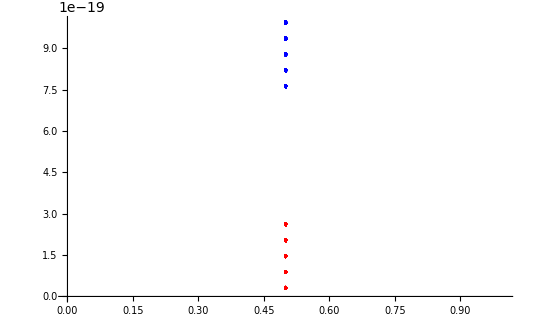

## Reference Guide

### Best Practices

Turn the second part of the following cell into a comment so that the cell can run. You can do this by adding (* before the part you want commented and *) after the part you want commented. Commenting is a good coding practice so that you know what you did and why you did it (also useful for other students or people if they are looking at your code)

```mathematica
x=5; this sets x equal to 5
```

debugging
commenting

### Units

A quick word on units: in a lot of the problems that you do over the course of the Pchem and Qchem semester units will be really important and one of the most frustrating things you’ll encounter is when your answer is really similar to the expected value but off by some order of magnitude or just off in general. A good place to start is by doing some dimensional analysis on your constants units and this can be helped by commenting your code with the units you expect as well as the units you are using.

### Getting Help and Useful Links

The first place to look for getting help is the Mathematica Documentation found here: https://reference.wolfram.com/language/. If the Documentation isn’t very clear or helpful (probably be the case) you should ask your fellow peers (if allowed) over Slack and if no one gets back to you in a reasonable time frame then feel free to directly Slack your TAs and/or Professors or @ them in the Slack where you posted your original question.

### Useful Commands and Shortcuts

#### Commands

For more information on these type as input in Mathematica and right click and select get help .

Other forms of visualization:

Show[g1,g2,...,] or Show[graphics,options] shows graphics with specified options added.

ListLinePlot[{y1,y2,...}] plots a line through the points {1,y1}, {2,y2}... or ListLinePlot[{{x1,y1},{x2,y2}...}] plots a line through a list of points with specific x and y positions

LogPlot[f,{x,xmin,xmax}] generates a log plot of f as a function of x from xmin to xmax

ContourPlot[f,{x,xmin,xmax},{y,ymin,ymax}] generates a contour plot of f as a function of x and y

ContourPlot3D[f,{x,xmin,xmax},{y,ymin,ymax},{z,zmin,zmax}] produces a 3-dimensional contour plot of f as a function of x,y, and z

Histogram[{x1,x2,...}] plots a histogram of the values xi

Piecewise[{{val1,cond1},{val2,cond2}...}] represents a piecewise function with values vali in the regions defined by the conditions condi.

Manipulate[expr, {u,umin,umax}] generates a version of expr with controls added to allow interactive manipulation of the value of u

Inequalities (give True or False as outputs):

Less: < (x < y yields True if x is determined to be less than y)

Greater: > (x > y yields True if x is determined to be greater than y)

LessEqual: <=, ≤ (x <= y yeilds True if x is determined to be less than or equal to y)

GreaterEqual: >=, ≥ (x >=y yields True if x is determined to be greater than or equal to y)

Unequal: !=, ≠ (lhs [left hand side] != rhs [right hand side] returns False if lhs and rhs are identical)

Between[x,{min,max}] is equivalent to min<=x<=max

Manipulating Lists, Tables, and Matrices:

Sort[list] sorts the elements of list into canonical order

SortBy[list, f] sorts the elements of list in the order defined by applying f to each of them

NumericalSort[list] sorts the elements of list into numerical order

AlphabeticSort[list] sorts the elements of list into alphabetical order

Riffle[{e1,e2,..},x] gives {e1,x,e2,x,..}

Transpose[list,{n1,n2,...}] transposes list so that the kth level in list is the nkth level in the result.

Tally[list] tallies the elements in list, listing all distinct elements together with their multiplicities

Count[list, pattern] gives the number of elements in list that match pattern

Flatten[list] flattens out nested lists

Miscellaneous
RandomInteger[{imin,imax}] gives a pseudorandom integer in the range{imin,imax}

Drop[list,n] gives list with its first n elements dropped

Import[source] imports data from source, returning a Wolfram Language representation of it

FindFit[data,expr,pars,vars] finds numerical values of the parameters prs that make expr give a best fit to data as a function of vars

Switch[expr,form1,value1,form2,value2,...] evaluates expr, then compares it with each of the formi in turn, evaluating and returning the valuei corresponding to the first match found

#### Shortcuts

#### Rowan add these in i dont know any

Tutorial and Reference Guide Developed by Rowan J. Goudy and Logan E. Smith